```mathematica
fileSEG = "C:\\Users\\Ali Hashmi\\Desktop\\3D segmentation fixed spheroid\\C0.res2";
Get@fileSEG;
```

## second image stack

```mathematica
secondChfile = "C:\\Users\\Ali Hashmi\\Desktop\\3D segmentation fixed spheroid\\C2.tif";
```

```mathematica
imageStackData[file_]:= Module[{bc,bc3D,roi},
bc=Import@file;
bc3D = Image3D[bc];
roi = ImageDimensions[bc3D];
Print@ImageAdjust[bc3D];
{roi,ImageData[bc3D]}
]
```

```mathematica
{roi,imageData}=imageStackData@secondChfile;
```

-Graphics3D-

## final analysis

```mathematica
Colorize@segNew
```

-Graphics3D-

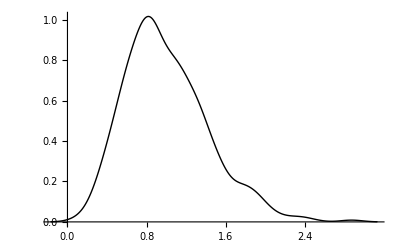

```mathematica
{areasM,centroidsM} = ComponentMeasurements[segNew,#]&/@{"Area","Centroid"};
SmoothHistogram[Values@#/(Mean@*Values@#),PlotStyle->{Thick,Black}]&@areasM
```

```mathematica
(* the block of code below allows us to create a nearest function from the segmentation structure. more specifically the nearest function is created using the points that represent each cell *)
```

```mathematica
innf=Reap[Module[{numberofcells,areasM=areasM,seg=segNew},
numberofcells = Length@areasM;
Do[
Sow[Thread[Position[seg,cellID]-> cellID]]
,{cellID,numberofcells}];
]][[2,1]];
```

```mathematica
nearestFunc=Nearest@Flatten[innf]
```

NearestFunction[{3, <>}]

```mathematica
(* lets get the signal from the second channel  above a certain threshold value (to eliminate background) as a simple vector of xyz positions and intensity. The threshold can be determined from imageHistogram *)
```

```mathematica
{signalxyzpos,signalIntensity}=Module[{minsignal=0.02,imgdata=imageData,signalxyzpos,signalIntensity},
signalxyzpos=Position[imgdata,x_/;x≥ minsignal];
signalIntensity = Extract[imgdata,signalxyzpos];
{signalxyzpos,signalIntensity}
];
```

```mathematica
IDs=Map[#~nearestFunc~{1,30}&,signalxyzpos];
IDs=Flatten[IDs/.{}-> {0}]; (* empty list -> background i.e. signal that does not belong to any nearest cell is assigned index 0 *)
```

```mathematica
cellIDVsSignal= DeleteCases[Partition[Riffle[IDs,signalIntensity],2],{0,_}];
```

```mathematica
ListPlot[cellIDVsSignal,PlotRange->All]
```

-Graphics-

```mathematica
{m1,m2,m3}=Mean[centroidsM[[All,2]]] (* centroid of the nuclei cluster *)
```

{267.184,104.207,32.2169}

```mathematica
(* this block allows us to extract signals corresponding to their respective nuclei as well as other information *)
```

```mathematica
result=Reap[Block[{centroidsM=centroidsM,cellIDList=cellIDVsSignal[[All,1]],signalList=cellIDVsSignal[[All,2]],cellID=Length@areasM,pos,sig,areasM=areasM,areaNuc,centroidNuc,m1=m1,m2=m2,m3=m3,disttocentre3d,disttocentre2d,heightNuc},
Do[
(pos=Position[cellIDList,i];
sig=Extract[signalList,pos];
areaNuc= areasM[[i,2]];
centroidNuc = centroidsM[[i,2]];
heightNuc = Last@centroidNuc;
disttocentre3d = EuclideanDistance[centroidNuc,{m1,m2,m3}];
disttocentre2d = EuclideanDistance[Most@centroidNuc,{m1,m2}];
Sow[{i,Length@sig,Mean[sig],StandardDeviation[sig],
areaNuc,centroidNuc,disttocentre3d,disttocentre2d,heightNuc}];
),{i,cellID}];
]][[2,1]];
```

## plotting graphs

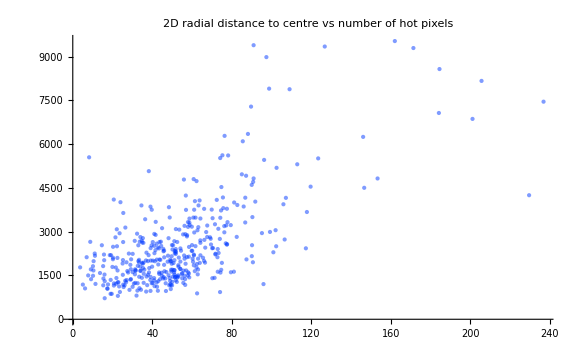

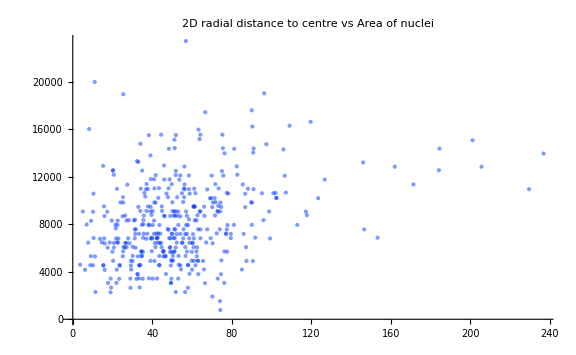

```mathematica
ListPlot[result[[All,{8,2}]],PlotLabel->"2D radial distance to centre vs number of hot pixels",PlotRange->All,ImageSize->Large,PlotStyle->{PointSize[Large],XYZColor[0,0,1,0.5]}]

ListPlot[result[[All,{8,5}]],PlotLabel-> "2D radial distance to centre vs Area of nuclei",PlotRange->All,ImageSize->Large,PlotStyle->{PointSize[Large],XYZColor[0,0,1,0.5]}]
```

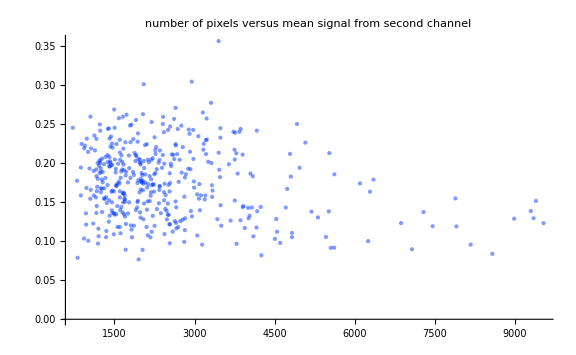

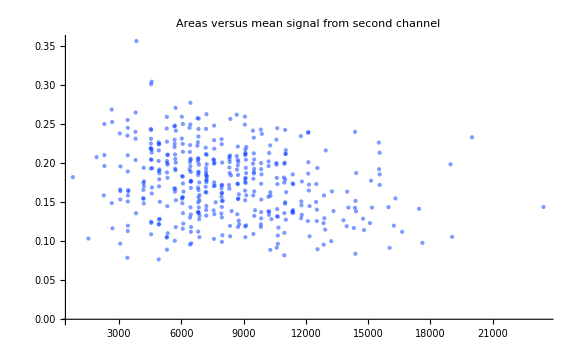

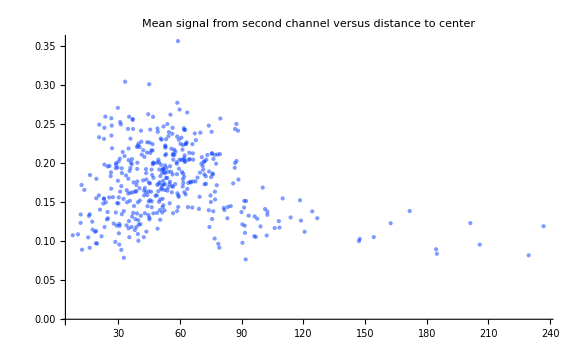

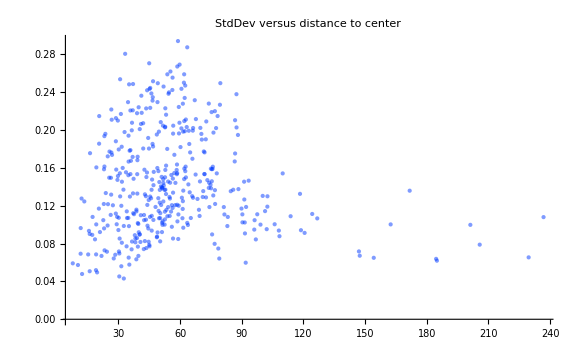

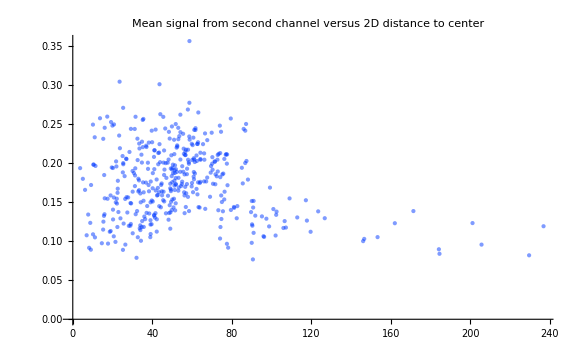

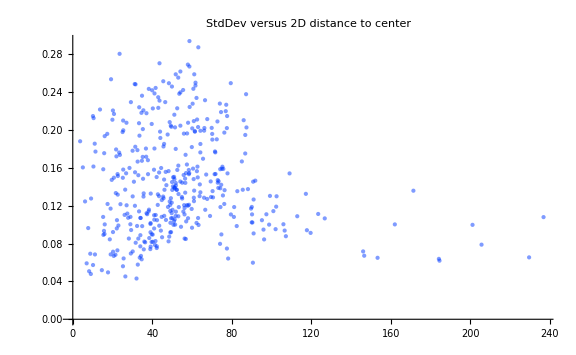

```mathematica
ListPlot[result[[All,{2,3}]],PlotLabel -> "number of pixels versus mean signal from second channel", PlotRange->All,ImageSize->Large,PlotStyle->{PointSize[Large],XYZColor[0,0,1,0.5]}]

ListPlot[result[[All,{5,3}]],PlotLabel->"Areas versus mean signal from second channel",PlotRange->All,ImageSize->Large,PlotStyle->{PointSize[Large],XYZColor[0,0,1,0.5]}]

ListPlot[result[[All,{7,3}]],PlotLabel->"Mean signal from second channel versus distance to center",PlotRange->All,ImageSize->Large,PlotStyle->{PointSize[Large],XYZColor[0,0,1,0.5]}]

ListPlot[result[[All,{7,4}]],PlotLabel->"StdDev versus distance to center",PlotRange->All,ImageSize->Large,PlotStyle->{PointSize[Large],XYZColor[0,0,1,0.5]}]

ListPlot[result[[All,{8,3}]],PlotLabel->"Mean signal from second channel versus 2D distance to center",PlotRange->All,ImageSize->Large,PlotStyle->{PointSize[Large],XYZColor[0,0,1,0.5]}]

ListPlot[result[[All,{8,4}]],PlotLabel->"StdDev versus 2D distance to center",PlotRange->All,ImageSize->Large,PlotStyle->{PointSize[Large],XYZColor[0,0,1,0.5]}]
```

## Signal from second channel - Radial distribution

```mathematica
ListPlot[result[[All,{8,3}]],PlotLabel->"Mean signal from second channel versus 2D distance to center",PlotRange->All,ImageSize->Large,PlotStyle->{PointSize[Large],XYZColor[0,0,1,0.5]}]
```

-Graphics-

FittedModel[0.190524-0.000282529 x]

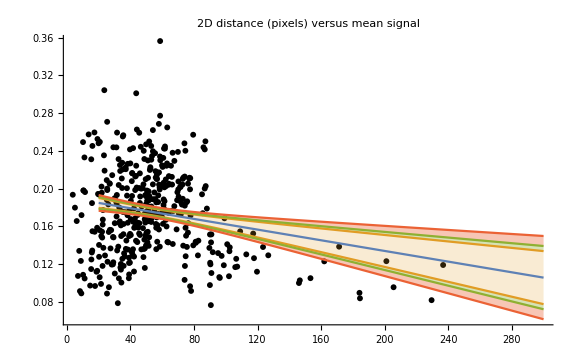

```mathematica
Clear[b];Clear[a];
data = result[[All,{8,3}]];
nlm = NonlinearModelFit[data,a+b*x,{a,b},x]

{bands90[_],bands95[_],bands99[_]} = Table[nlm["MeanPredictionBands",ConfidenceLevel-> c1],{c1,{.90,.95,.99}}];

Show[
ListPlot[data,PlotStyle->Black],
Plot[{nlm[x],bands90[x],bands95[x],bands99[x]},{x,20,300},Filling-> {2-> {1},3->{2},4-> {3},5-> {4}}],PlotRange->All,
PlotLabel->Style["2D distance (pixels) versus mean signal",{FontSize->18,Black}],ImageSize-> Large]
```

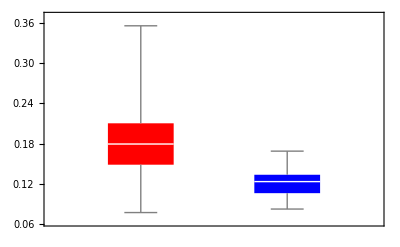

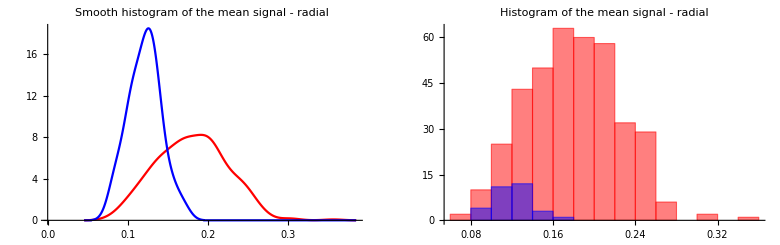

```mathematica
outint = (Extract[#,Position[#[[All,1]],x_/;x>94]]&@data)[[All,2]];
inint = (Extract[#,Position[#[[All,1]],x_/;x≤ 94]]&@data)[[All,2]];

BoxWhiskerChart[{inint,outint},ChartStyle->{Red,Blue}]

GraphicsRow[
{
SmoothHistogram[{inint,outint}, PlotLabel->"Smooth histogram of the mean signal - radial",PlotStyle-> {Red,Blue}],Histogram[{inint,outint},PlotLabel-> "Histogram of the mean signal - radial",ChartStyle->{Red,Blue},ImageSize->Medium]
}
]
```

## Signal from second channel as a function of height of nuclei cluster

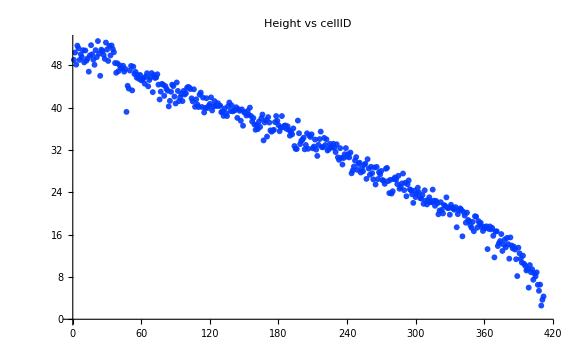

```mathematica
ListPlot[result[[All,9]],PlotRange->All,PlotLabel->"Height vs cellID",PlotStyle->XYZColor[0,0,1,0.9],ImageSize->Large]
```

```mathematica
Show[SetAlphaChannel[-Graphics3D-,0.008],Graphics3D[{Darker@Green,Sphere[{m1,m2,m3},5]}]]
```

-Graphics3D-

```mathematica
(* collagen is near 50, 1 is the top *)
```

FittedModel[0.241365-0.00205201 x]

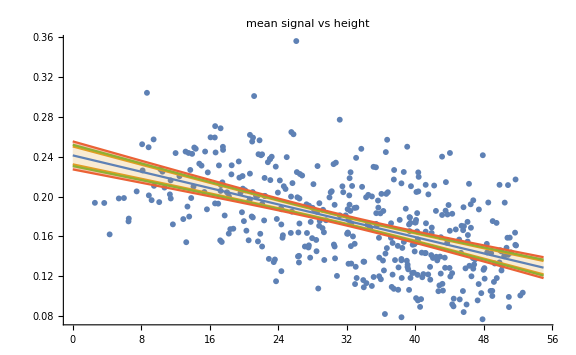

```mathematica
Clear[a,b];
data = result[[All,{9,3}]]; (* height and mean signal *)

nlm=NonlinearModelFit[data,a+b*x,{a,b},x]

{bands90[x_],bands95[x_],bands99[x_]} = Table[nlm["MeanPredictionBands",ConfidenceLevel-> c1],{c1,{.90,.95,.99}}];

Show[
ListPlot[data],
Plot[{nlm[x],bands90[x],bands95[x],bands99[x]},{x,0,55},Filling-> {2-> {1},3->{2},4-> {3},5-> {4}}],PlotRange->All,
PlotLabel->Style[#,{FontSize->18,Black}]&@"mean signal vs height",ImageSize-> Large]
```

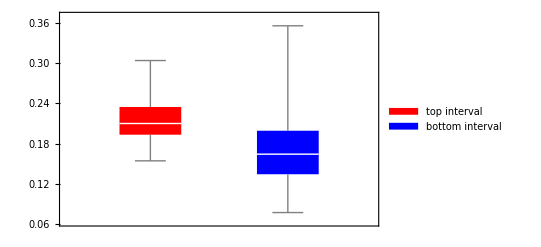

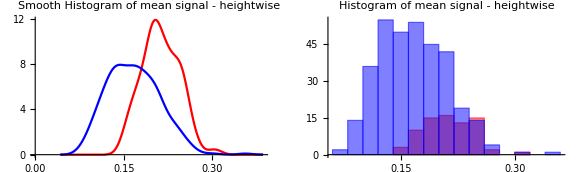

8.65663×10^-20

```mathematica
topint = (Extract[#,Position[#[[All,1]],x_/;x<20]]&@data)[[All,2]];
bottomint = (Extract[#,Position[#[[All,1]],x_/;x≥20]]&@data)[[All,2]];

BoxWhiskerChart[{topint,bottomint},ChartStyle->{Red,Blue},ChartLegends->{"top interval","bottom interval"}]

GraphicsRow[{
SmoothHistogram[{topint,bottomint},PlotLabel->"Smooth Histogram of mean signal - heightwise",PlotStyle->{Red,Blue}],
Histogram[{topint,bottomint},PlotLabel->"Histogram of mean signal - heightwise",ChartStyle->{Red,Blue}]
},
 ImageSize->Large]

TTest[{topint,bottomint},0]
```